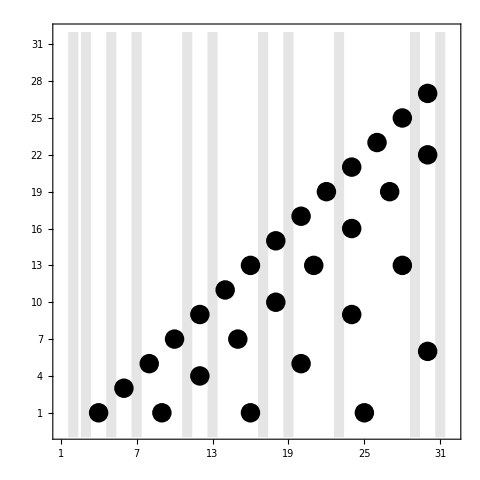

```mathematica
(*Generate all composite points up to n*)comp1[m_,n_]:=Join@@Table[{k*p+p^2,k*p+1},{k,0,n},{p,Max[1,Ceiling[1/2 (-k+Sqrt[k^2+4*m])]],Floor[1/2 (-k+Sqrt[k^2+4*n])]}]
(*Visualize the forest*)
lpl[hi_]:=ListPlot[GatherBy[Select[#[[2;;]],#[[1]]>#[[2]]&],PrimeQ@*First],
PlotRange->{{1,32},{-1/2,32}},AxesOrigin->{0,0},AspectRatio->1,PlotMarkers->{Automatic,Large},Frame->True,GridLines->{Range@hi-1/2,Range[0,hi]-1/2},FrameTicks->{{Range[hi],None},{Range[hi],None}},PlotStyle->Black, ImageSize->{480,480},(*PlotLabel->Row@{Style["Primal Forest",Bold]," (up to 31)"},*)Epilog->{Thick,Dashed,Black,FaceForm@Opacity@0.1,Rectangle[{First@#-0.4,-1},{First@#+0.4,32}]&/@Select[#,PrimeQ@*First]}]&@comp1[1,hi]
(*Generate the plot*)
lpl@31
```

```mathematica
comp1[1,31]
```

{{1,1},{4,1},{9,1},{16,1},{25,1},{2,2},{6,3},{12,4},{20,5},{30,6},{3,3},{8,5},{15,7},{24,9},{4,4},{10,7},{18,10},{28,13},{5,5},{12,9},{21,13},{6,6},{14,11},{24,16},{7,7},{16,13},{27,19},{8,8},{18,15},{30,22},{9,9},{20,17},{10,10},{22,19},{11,11},{24,21},{12,12},{26,23},{13,13},{28,25},{14,14},{30,27},{15,15},{16,16},{17,17},{18,18},{19,19},{20,20},{21,21},{22,22},{23,23},{24,24},{25,25},{26,26},{27,27},{28,28},{29,29},{30,30},{31,31}}

```mathematica
?Rectangle
```